## Unified Compositional Semantics for (Multiway) Causality

### What is Causality?

Partial order: transitivity; reflexivity/antisymmetry/acyclicity

### Different Notions of Causality (Technical)

#### Fundamental Physics

Special/General Relativity (Penrose - Differential Topological Techniques for GR; Malament’s Theorem/Malament-Hawking-McCarthy-King(?) Theorem) - potential for information exchange? Partial order model of causality, etc.

```mathematica
sprinkling=ResourceFunction["FlatSpacetimeSprinkling"][2,100]
```

SpacetimeSprinkling[…]

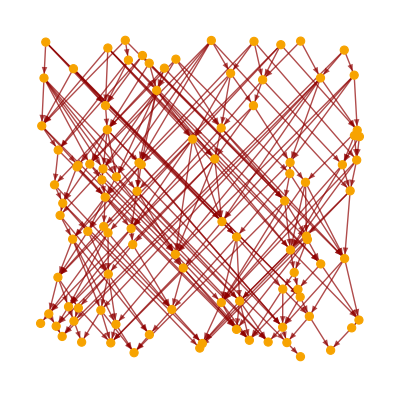

```mathematica
sprinkling["CausalGraph"]
```

Quantum Mechanics (esp. quantum information theory/”quantum computing”).

“Indefinite causal order” (i.e. “superpositions” of quantum circuits with non-isomorphic causal structures, as per Brukner).

```mathematica
gate1=ResourceFunction["QuantumDiscreteOperator"]["Hadamard",{1}]
```

QuantumDiscreteOperator[…]

```mathematica
gate2=ResourceFunction["QuantumDiscreteOperator"]["PauliZ",{1}]
```

QuantumDiscreteOperator[…]

```mathematica
gate3=ResourceFunction["QuantumDiscreteOperator"]["PauliZ",{2}]
```

QuantumDiscreteOperator[…]

```mathematica
circuit=ResourceFunction["QuantumCircuitOperator"][{gate1,gate2},{2}]
```

QuantumCircuitOperator[…]

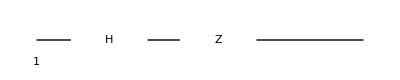

```mathematica
circuit["Diagram"]
```

```mathematica
circuit["Operator"]
```

<|0⊗0→1/(√2),0⊗1→-1/(√2),1⊗0→1/(√2),1⊗1→1/(√2)|>

```mathematica
circuit2=ResourceFunction["QuantumCircuitOperator"][{gate1,gate3},{2}]
```

QuantumCircuitOperator[…]

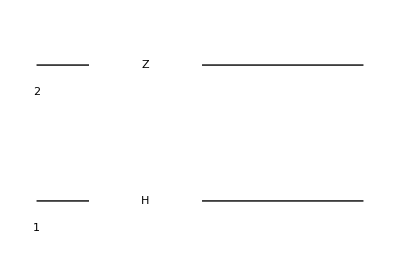

```mathematica
circuit2["Diagram"]
```

```mathematica
circuit2["Operator"]
```

<|(0⊗0)⊗(0⊗0)→1/(√2),(0⊗0)⊗(0⊗1)→0,(0⊗0)⊗(1⊗0)→1/(√2),(0⊗0)⊗(1⊗1)→0,(0⊗1)⊗(0⊗0)→0,(0⊗1)⊗(0⊗1)→-1/(√2),(0⊗1)⊗(1⊗0)→0,(0⊗1)⊗(1⊗1)→-1/(√2),(1⊗0)⊗(0⊗0)→1/(√2),(1⊗0)⊗(0⊗1)→0,(1⊗0)⊗(1⊗0)→-1/(√2),(1⊗0)⊗(1⊗1)→0,(1⊗1)⊗(0⊗0)→0,(1⊗1)⊗(0⊗1)→-1/(√2),(1⊗1)⊗(1⊗0)→0,(1⊗1)⊗(1⊗1)→1/(√2)|>

#### Distributed Systems/Parallel Computing/Concurrency/etc.

Place/Transition nets, Petri nets, models of packet switching networks, etc.

(c.f. Lamport, ordering of events in distributed systems, “logical clocks”, “synchronization”, etc., made concrete connections to fundamental physics, esp. general relativity)

#### Chemistry/Chemical Reaction Networks/Biochemistry(??)

Relations to catalysis? (Connection to Deutsch/Marletto, constructor theory, etc.)

Generalized models of activation kinetics (Michaelis-Menten(!!??) law?)

#### Causality in (Algebraic) Graph Rewriting/Graph Grammars

Direct relation to Wolfram model, hypergraph rewriting, etc.

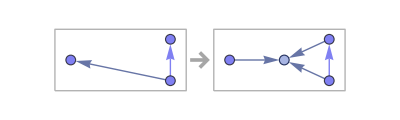

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}]]
```

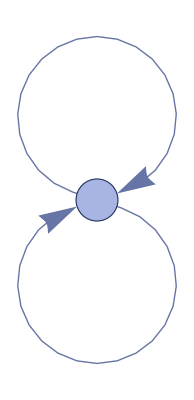
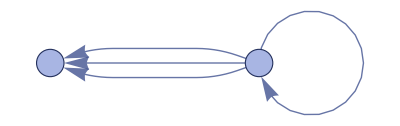
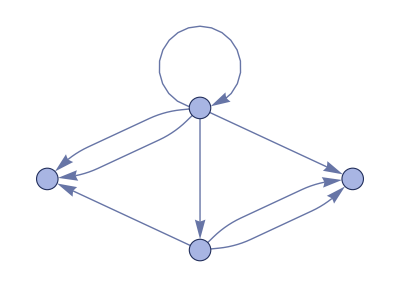
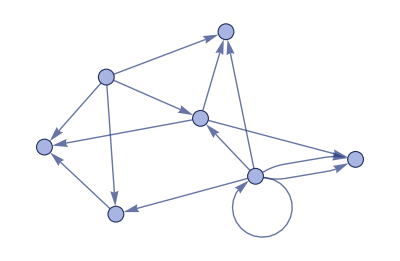
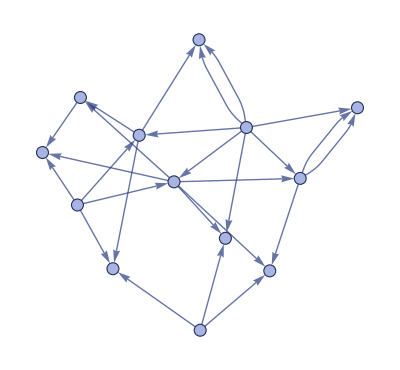

```mathematica
ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}},{{1,1},{1,1}},4]["StatesPlotsList"]
```

```mathematica
evolution=ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}},{{1,1},{1,1}},4]
```

WolframModelEvolutionObject[…]

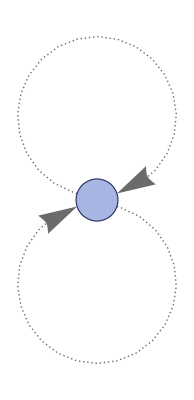
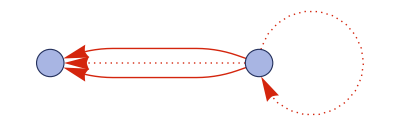
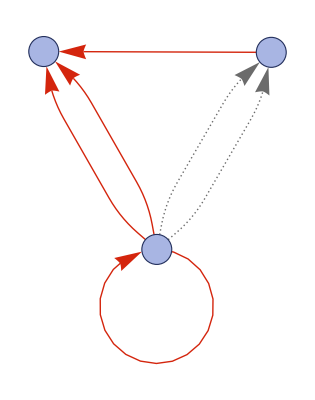
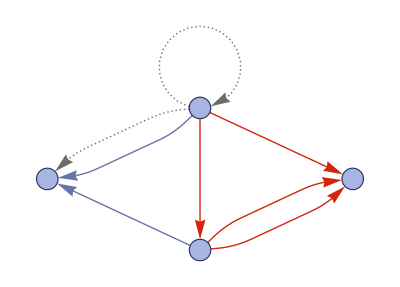
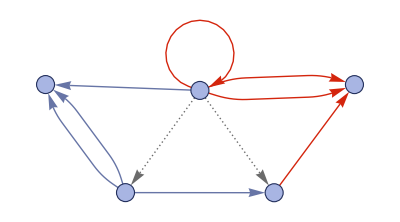
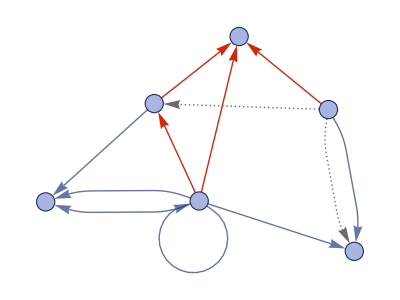
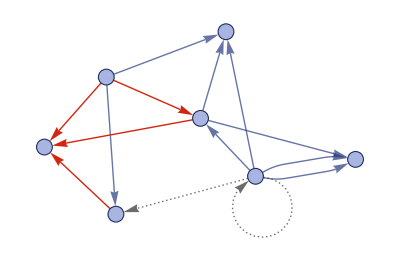
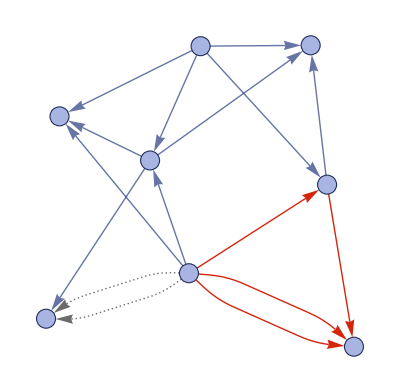

```mathematica
evolution["EventsStatesPlotsList"]
```

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}},{{{1,1},{1,1}}},3,"CausalGraph",VertexSize->1]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}},{{{1,1},{1,1}}},2]
```

{{{{1,1},{1,1}}},{{{1,1},{1,2},{1,2},{1,2}}},{{{1,1},{1,2},{1,2},{1,3},{1,3},{2,3}},{{1,2},{1,2},{1,2},{1,3},{1,3},{2,3}},{{1,1},{1,2},{1,2},{1,3},{2,3},{2,3}}}}

```mathematica
{{1,2},{1,2},{1,2},{1,3},{1,3},{2,3}}
```

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}},{{{1,1},{1,1}}},2,"StatesGraph",VertexSize->1]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}},{{{1,1},{1,1}}},2,"EvolutionCausalGraph",VertexSize->1]
```

-Graphics-

Allows for “spurious” causal relations. (I.e. you can have events that merely “touch” a hyperedge/token, but do not structurally modify it in any interesting way.)

Relationship to individual vs. collective token semantics (and token deduplication, etc.) in the theory of P/T nets(???)

#### Statistical Inference

Determining potential causal relationships between events using Bayesian reasoning (e.g. Bayesian causal networks?).

### Philosophical Questions about Causality?

Hume/Russell/etc. questioning whether causal relationships between events can even be ascertained empirically? (Can only be determined probabilistically??)

Can causality be defined in a non-counterfactual way? (Can causality even be defined for deterministic event systems?)

```mathematica
ResourceFunction["MultiwayTuringMachine"][{2506},{{1,1,0},{0,0,1,0,0}},5,"StatesGraph",VertexSize->1]
```

-Graphics-

```mathematica
ResourceFunction["MultiwayTuringMachine"][{2506},{{1,1,0},{0,0,1,0,0}},5,"CausalGraph",VertexSize->1]
```

-Graphics-

### Big Picture Conjecture

Thinking about multiway systems as (concrete computational semantics for) symmetric monoidal categories...

Perhaps, causality is a consequence of the existence of sequential compositions that cannot be “collapsed” into tensor products(??)

“Unrolling” of tensor products into sequential compositions (i.e. “unrolling” of branchial graphs into compositions of individual multiway histories/threads/etc.): always possible.

But, there are obstructions to “collapsing” sequential compositions into tensor products (i.e. “collapsing” sequentially-composed multiway histories/threads/etc. into branchial graphs).

Conjecture(!): these obstructions give us a general algebraic/compositional/functorial definition of causality in arbitrary multiway systems.

```mathematica
category=ResourceFunction["AbstractCategory"][<|g1->{Z,X},g2->{Z,X},f->{X,Y}|>,{},{CircleDot[f,g1]==CircleDot[f,g2],g1==g2}]
```

AbstractCategory[…]

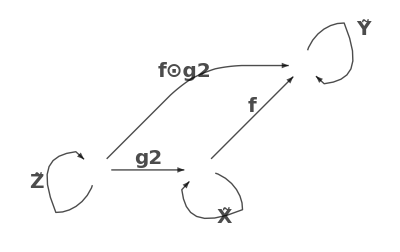

```mathematica
category["ReducedLabeledGraph"]
```

```mathematica
category["Monomorphisms"]
```

<|g1→True,g2→True,f→True,f⊙g1→True,f⊙g2→True,Z̃→True,X̃→True,Ỹ→True|>

```mathematica
category2=ResourceFunction["AbstractCategory"][<|f->{X,Y},g->{X,Z}|>]
```

AbstractCategory[…]

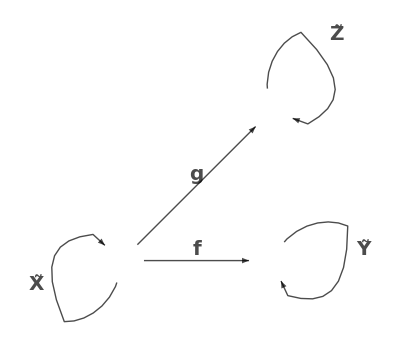

```mathematica
category2["FullLabeledGraph"]
```

```mathematica
pushout=ResourceFunction["AbstractPushout"][<|f->{T,A},g->{T,B}|>]
```

AbstractPushout[…]

```mathematica
pushout["PushoutEquations"]
```

{i_1⊙f==i_2⊙g}

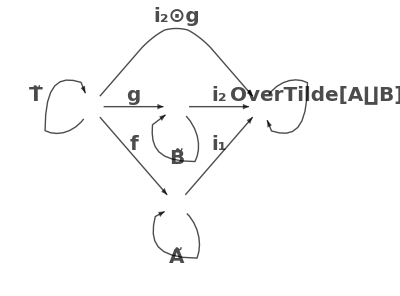

```mathematica
pushout["ReducedLabeledGraph"]
```

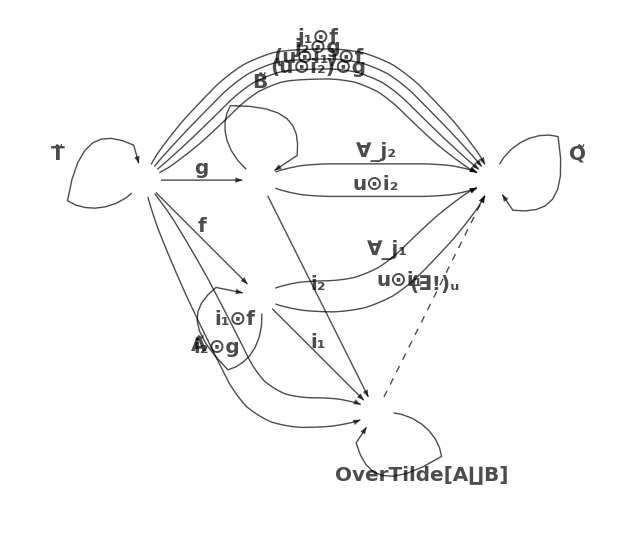

```mathematica
pushout["UniversalFullLabeledGraph"]
```

```mathematica
pushout["UniversalPushoutEquations"]
```

{i_1⊙f==i_2⊙g,∀_{j_1,j_2}(i_1⊙f==i_2⊙g⇒∃_u j_1==u⊙i_1),∀_{j_1,j_2}(i_1⊙f==i_2⊙g⇒∃_u j_2==u⊙i_2)}

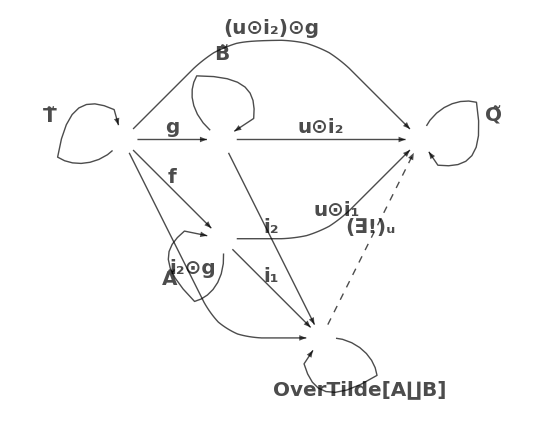

```mathematica
pushout["UniversalReducedLabeledGraph"]
```

### Connection to Place/Transition Nets, Monoids, Petri Net Algebras, etc.

```mathematica
petriNet=ResourceFunction["MakePetriNet"][<|"Places"->{a,b,c},"Transitions"->{t1,t2,t3},"Arcs"->{a->t1,b->t2,c->t3,t2->c,t3->b,t1->b}|>,{2,0,0}]
```

PetriNetObject[…]

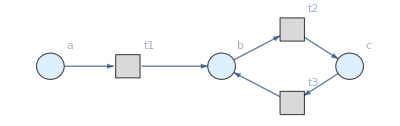

```mathematica
petriNet["UnlabeledGraph"]
```

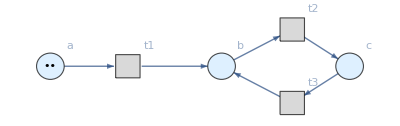

```mathematica
petriNet["LabeledGraph"]
```

```mathematica
ResourceFunction["MultiwayPetriNet"][petriNet,2,"StatesGraph",VertexSize->1]
```

-Graphics-

```mathematica
ResourceFunction["MultiwayPetriNet"][petriNet,2,"EvolutionCausalGraph",VertexSize->1]
```

-Graphics-

Step sequences vs. occurrence sequences (vs. unfoldings?)